## Mirror machine model given in the Garren et al (1958); Gibson et al (1963)

### Expressions for the field and other GCM quantities

```mathematica
Clear["Global`*"]
k = 2*π/L;
A[r_,θ_,z_]={0,(1/2.)*B0*r - ((B0*α*L)/(2*π))*Cos[k*z]*BesselI[1,k*r] ,0};
curlA[r_,θ_,z_]=Curl[A[r,θ,z],{r,θ,z},"Cylindrical"];
fieldCyl[r_,θ_,z_]={-B0 α BesselI[1,k r] Sin[k z],0,B0*(1 - α*BesselI[0,k r]*Cos[k z])}
fieldCar[x_,y_,z_]=fieldCyl[r,θ,z]/.{r-> Sqrt[x^2+y^2],θ->ArcTan[x,y],z-> z}
(*field[r_,θ_,z_] = curlA[r,θ,z]//.{BesselI[1,k r]/r->(k/2)*(BesselI[0,k r]- BesselI[2,k r])};*)
curlField =Simplify[MatrixForm[Curl[fieldCyl[r,θ,z],{r,θ,z},"Cylindrical"]]];
divField = FullSimplify[MatrixForm[Div[fieldCyl[r,θ,z],{r,θ,z},"Cylindrical"]]]
fieldMagCyl[r_,θ_,z_]=Sqrt[Dot[fieldCyl[r,θ,z],fieldCyl[r,θ,z]]];
fieldMagCar[x_,y_,z_]=fieldMagCyl[r,θ,z]/.{r-> Sqrt[x^2+y^2],θ->ArcTan[x,y],z-> z};
totalEnergyCar[x_,y_,z_,vpar_]= 0.5*vpar^2 + fieldMagCar[x,y,z];
totalEnergyCyl[r_,θ_,z_,vpar_]= 0.5*vpar^2 + fieldMagCyl[r,θ,z];
(*b[x_,y_,z_] =field[x,y,z]/fieldMag[x,y,z];
gradModB[x_,y_,z_]=Grad[fieldMag[x,y,z],{x,y,z}]//.{BesselI[1,k Sqrt[x^2+y^2]]/Sqrt[x^2+y^2]->(k/2)*(BesselI[0,k Sqrt[x^2+y^2]]- BesselI[2,k Sqrt[x^2+y^2]])};
gradModB[0,0,0]
bCrossGradModB[x_,y_,z_] = Cross[b[x,y,z],gradModB[x,y,z]]; 
curlb[x_,y_,z_] = Curl[b[x,y,z],{x,y,z}]/.{BesselI[1,k Sqrt[x^2+y^2]]/Sqrt[x^2+y^2]->(k/2)*(BesselI[0,k Sqrt[x^2+y^2]]- BesselI[2,k Sqrt[x^2+y^2]])};
curlb[0,0,0]
tildeB[x_,y_,z_,vpar_]=field[x,y,z] +Sqrt[mutilde]*vpar*curlb[x,y,z];
tildeB[0,0,0,0]
tildeBpar[x_,y_,z_,vpar_] = Dot[tildeB[x,y,z,vpar], b[x,y,z]];
tildeBpar[0,0,0,0]*)
```

{-B0 α BesselI[1,(2 π r)/L] Sin[(2 π z)/L],0,B0 (1-α BesselI[0,(2 π r)/L] Cos[(2 π z)/L])}

{-B0 α BesselI[1,(2 π √(x^2+y^2))/L] Sin[(2 π z)/L],0,B0 (1-α BesselI[0,(2 π √(x^2+y^2))/L] Cos[(2 π z)/L])}

0

### Simplify fails to get rid of the r = 0 singularity but I manipulated by hand to remove r = 0

```mathematica
Simplify[curlA[r,θ,z]]//.{BesselI[1,k r]/r->(k/2)*(BesselI[0,k r]- BesselI[2,k r])}
fieldMagCyl[0.,θ,z]//Simplify
```

{-B0 α BesselI[1,(2 π r)/L] Sin[(2 π z)/L],0,B0 (1.-0.5 α BesselI[0,(2 π r)/L] Cos[(2 π z)/L]-0.5 α (BesselI[0,(2 π r)/L]-BesselI[2,(2 π r)/L]) Cos[(2 π z)/L]-0.5 α BesselI[2,(2 π r)/L] Cos[(2 π z)/L])}

√((B0-1. B0 α Cos[(2 π z)/L])^2)

### Solving for the critical surfaces in the field, that is d | B | /ds = 0

```mathematica
B0=2.0;α=0.1;L =2.;
b[r_,θ_,z_]=fieldCyl[r,θ,z]/fieldMagCyl[r,θ,z];
fieldMinPt = FindMinimum[fieldMagCyl[r,θ,z],{{r,1.},{z,0.}}]
gradModB[r_,θ_,z_]=Grad[fieldMagCyl[r,θ,z],{r,θ,z},"Cylindrical"];
dmodBds[r_,θ_,z_] = Dot[b[r,θ,z],gradModB[r,θ,z]];
dmodBds[x_,y_,z_]=dmodBds[r,θ,z]/.{r->Sqrt[x^2 +y^2],θ->ArcTan[x,y],z->z};
graddmodBds[r_,θ_,z_]=Grad[dmodBds[r,θ,z],{r,θ,z},"Cylindrical"];
d2modBds2[r_,θ_,z_] = Dot[b[r,θ,z],graddmodBds[r,θ,z]];
d2modBds2[x_,y_,z_]=d2modBds2[r,θ,z]/.{r->Sqrt[x^2 +y^2],θ->ArcTan[x,y],z->z};
(*ContourPlot[dmodBds[r,0,z],{r,0,1},{z,-1.5 L/2,1.5 L/2},Contours->{0},ContourShading->None]*)
sigmaPlot3d =ContourPlot3D[dmodBds[x,y,z],{x,-fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2],fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2]},{y,-fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2],fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2]},{z,-1.5 L/2,1.5 L/2},Contours ->{0},ContourStyle->Directive[Blue,Opacity[0.8],Specularity[White,30]],PlotPoints->5,MaxRecursion->1,PlotTheme->{"Scientific"},AxesLabel->{Style[x,25],Style[y,25],Style[z,25]},FaceGrids->{{0,0,-1},{0,1,0},{-1,0,0}},Mesh-> None,MeshStyle->Gray,ImageSize->Medium]
(*sigmaPlot3d =ContourPlot3D[dmodBds[x,y,z],{x,-0.75,0.75},{y,-0.75,0.75},{z,-1.25 L/2,1.25 L/2},Contours ->{0},PlotPoints->5,MaxRecursion->1,PlotTheme->{"Scientific"},AxesLabel->{Style[x,25],Style[y,25],Style[z,25]},FaceGrids->{{0,0,-1},{0,1,0},{-1,0,0}},Mesh-> 5,MeshStyle->Gray,ImageSize->Medium]*)
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{3.77476×10^-15,{r→1.22798,z→0.}}

-Graphics3D-

### Visualizing the field magnitude

```mathematica
B0=2.;α=0.1;L = 2.;
h0=fieldMagCyl[0,0,L/2]
h1=fieldMagCyl[0,0,-L/2]
cplot3d=ContourPlot3D[fieldMagCar[x,y,z],{x,-1.5,1.5},{y,-1.5,1.5},{z,-1.25 L/2,1.25 L/2},Contours->{h0+0.01*h0},PlotPoints->5,MaxRecursion->2,ContourStyle->{{Directive[FaceForm[Orange,Red],Opacity[0.5]]}},PlotTheme->{"Scientific"},AxesLabel->{Style[x,28],Style[y,28],Style[z,28]},FaceGrids->{{0,0,-1},{0,1,0},{-1,0,0}},Mesh-> None,MeshStyle->Gray,AxesStyle->Directive[Gray,FontSize->20],ImageSize->Large];
Show[sigmaPlot3d,cplot3d,PlotRange->{{-1.5,1.5},{-1.5,1.5},{-1.25 L/2,1.25 L/2}},PlotTheme->{"Scientific"},AxesLabel->{Style[x,32],Style[y,32],Style[z,32]},FaceGrids->{{0,0,-1},{0,1,0},{-1,0,0}},Mesh-> None,MeshStyle->Gray,AxesStyle->Directive[Gray,FontSize->25],ImageSize->Large]
```

2.2

2.2

-Graphics3D-

2.2

2.2

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{3.77476×10^-15,{r→1.22798,z→0.}}

√(4. (1-0.1 BesselI[0,3.14159 r] Cos[3.14159 z])^2+0.04 BesselI[1,3.14159 r]^2 Sin[3.14159 z]^2)

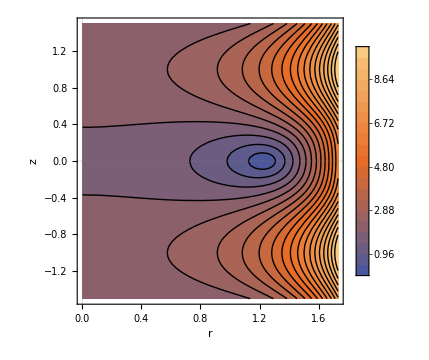

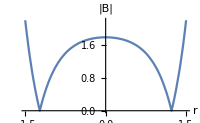
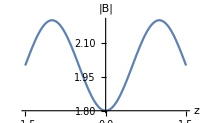

```mathematica
B0=2.;α=0.1;L = 2.;
h0=Norm[fieldMagCyl[0,0,L/2]]
h1=Norm[fieldMagCyl[0,0,-L/2]]
(*fieldZeroPt=FindRoot[fieldMagCyl[r,0,0],{r,1.2}];
Print[fieldZeroPt[[1]][[2]],"; |B|=",fieldMagCyl[r,0,0]/.fieldZeroPt ]
fieldZeroPt=FindRoot[{D[fieldMagCyl[r,0,z],r]==0,D[fieldMagCyl[r,0,z],z]==0},{{r,1.5},{z,0.001}}];
Print[fieldZeroPt,"; |B|=",fieldMagCyl[r,0,0]/.fieldZeroPt ]*)
fieldMinPt = FindMinimum[fieldMagCyl[r,θ,z],{{r,1.},{z,0.}}]
fieldMagCyl[r,θ,z]
ContourPlot[fieldMagCyl[r,0,z],{r,0,Sqrt[3]},{z,-1.5*(L/2),1.5*(L/2)},Contours->20,PlotPoints->10,MaxRecursion->2,FrameLabel->{Style[r,25,GrayLevel[0]],Style[z,25,GrayLevel[0]]},PlotLegends->Automatic,Mesh-> 5,MeshStyle->Gray,PlotTheme->"Scientific",ImageSize->Medium]
{Plot[fieldMagCyl[r,0,0],{r,-1.5,1.5},AxesLabel->{r,"|B|"},LabelStyle->{10,GrayLevel[0]},ImageSize->200],Plot[fieldMagCyl[0,0,z],{z,-1.5,1.5},AxesLabel->{z,"|B|"},LabelStyle->{10,GrayLevel[0]},ImageSize->200]}
```

```mathematica
cplot2d =ContourPlot[fieldMagCyl[r,0,z],{r,0,√3},{z,1/2 (-1.5) L,(1.5 L)/2},PlotTheme->"Scientific",Contours->20,PlotPoints->10,MaxRecursion->2,FrameLabel->{Style[r,25,GrayLevel[0]],Style[z,25,GrayLevel[0]]},PlotLegends->Automatic,Mesh->5,MeshStyle->GrayLevel[0.5],ImageSize->Medium]
(*Export["~/Documents/magnetic-mirror/modB-axisym-z0sym.png",cplot2d,"PNG"]*)
```

-Graphics-

2.2

2.2

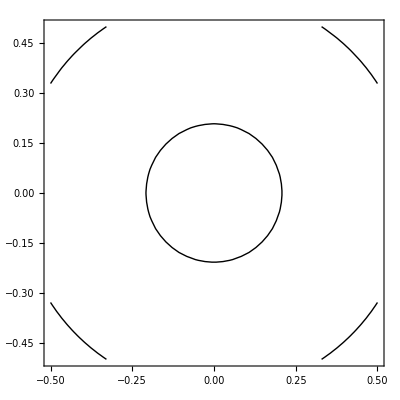

```mathematica
B0=2.;α=0.1;L = 2.;
h0=fieldMagCyl[0,0,L/2.]
h1=fieldMagCyl[0,0,-L/2.]
ContourPlot[fieldMagCar[x,y,L/2],{x,-0.5,0.5},{y,-0.5,0.5},Contours->{(h0+0.01*h0),(h0+0.1*h0)},ContourShading->None]
```

```mathematica
B0=2;α=0.1;L = 2.;
(*StreamPlot3D[field[x,y,z],{x,-1,1},{y,-1,1},{z,-L,L},
PlotLegends->Automatic,StreamPoints->RandomReal[{-1,1},{30,3}],
PlotTheme->"Scientific",FaceGrids->{{0,0,-1},{0,1,0},{-1,0,0}},RegionFunction->Function[{x,y,z},x^2+y^2≤2]]*)
StreamPlot3D[fieldCar[x,y,z],{x,-0.5,0.5},{y,-0.5,0.5},{z,-1.5 L/2,1.5 L/2},
StreamPoints->RandomReal[{-0.3,0.3},{10,3}],AxesLabel->{Style[x,25],Style[y,25],Style[z,25]},
PlotTheme->"Scientific",FaceGrids->{{0,0,-1},{0,1,0},{-1,0,0}},ImageSize->400]
```

-Graphics3D-

### First-order guiding center motion

```mathematica
B0=2.0;α=0.1;L =2.;mutilde = 1.;
modB[x_,y_,z_] = fieldMagCar[x,y,z];
b[x_,y_,z_] =fieldCar[x,y,z]/modB[x,y,z];
gradModB[x_,y_,z_]= Simplify[Grad[modB[x,y,z],{x,y,z}]];
bCrossGradModB[x_,y_,z_] = Cross[b[x,y,z],gradModB[x,y,z]] ;
curlb[x_,y_,z_] = Curl[b[x,y,z],{x,y,z}];
tildeB[x_,y_,z_,vpar_]=fieldCar[x,y,z] +Sqrt[mutilde]*vpar*curlb[x,y,z];
tildeBpar[x_,y_,z_,vpar_] = Dot[tildeB[x,y,z,vpar], b[x,y,z]];
Eqn1=x'[t]==(vpar[t]*tildeB[x[t],y[t],z[t],vpar[t]][[1]] + Sqrt[mutilde]*bCrossGradModB[x[t],y[t],z[t]][[1]])/tildeBpar[x[t],y[t],z[t],vpar[t]];
Eqn2=y'[t]==(vpar[t]*tildeB[x[t],y[t],z[t],vpar[t]][[2]] + Sqrt[mutilde]*bCrossGradModB[x[t],y[t],z[t]][[2]])/tildeBpar[x[t],y[t],z[t],vpar[t]];
Eqn3=z'[t]==(vpar[t]*tildeB[x[t],y[t],z[t],vpar[t]][[3]] + Sqrt[mutilde]*bCrossGradModB[x[t],y[t],z[t]][[3]])/tildeBpar[x[t],y[t],z[t],vpar[t]];
Eqn4=vpar'[t]==-(Dot[tildeB[x[t],y[t],z[t],vpar[t]],gradModB[x[t],y[t],z[t]]])/tildeBpar[x[t],y[t],z[t],vpar[t]];
eqpt=FindRoot[{Eqn1,Eqn2,Eqn3,Eqn4}/.{x'[t]->0,y'[t]->0,z'[t]->0,vpar'[t]->0},{{x[t],10.^-12},{y[t],10.^-16},{z[t],0.9},{vpar[t],0}}]
(*B0=2.0;α=0.1;L =2.;
mutilde = 10.^-4;
modB[r_,θ_,z_] = fieldMagCyl[r,θ,z];
b[r_,θ_,z_] =fieldCyl[r,θ,z]/modB[r,θ,z];
gradModB[r_,θ_,z_]= Simplify[Grad[modB[r,θ,z],{r,θ,z},"Cylindrical"]];
bCrossGradModB[r_,θ_,z_] = Cross[b[r,θ,z],gradModB[r,θ,z]] ;
curlb[r_,θ_,z_] = Curl[b[r,θ,z],{r,θ,z}];
tildeB[r_,θ_,z_,vpar_]=fieldCyl[r,θ,z] +Sqrt[mutilde]*vpar*curlb[r,θ,z];
tildeBpar[r_,θ_,z_,vpar_] = Dot[tildeB[r,θ,z,vpar], b[r,θ,z]];
Eqn1=r'[t]==(vpar[t]*tildeB[r[t],θ[t],z[t],vpar[t]][[1]] + Sqrt[mutilde]*bCrossGradModB[r[t],θ[t],z[t]][[1]])/tildeBpar[r[t],θ[t],z[t],vpar[t]];
Eqn2=θ'[t]==(vpar[t]*tildeB[r[t],θ[t],z[t],vpar[t]][[2]] + Sqrt[mutilde]*bCrossGradModB[r[t],θ[t],z[t]][[2]])/(r[t]*tildeBpar[r[t],θ[t],z[t],vpar[t]]);
Eqn3=z'[t]==(vpar[t]*tildeB[r[t],θ[t],z[t],vpar[t]][[3]] + Sqrt[mutilde]*bCrossGradModB[r[t],θ[t],z[t]][[3]])/tildeBpar[r[t],θ[t],z[t],vpar[t]];
Eqn4=vpar'[t]==-(Dot[tildeB[r[t],θ[t],z[t],vpar[t]],gradModB[r[t],θ[t],z[t]]])/tildeBpar[r[t],θ[t],z[t],vpar[t]];
eqpt=FindRoot[{Eqn1,Eqn2,Eqn3,Eqn4}/.{r'[t]->0,θ'[t]->0,z'[t]->0,vpar'[t]->0},{{r[t],10.^-16},{θ[t],0},{z[t],1.0},{vpar[t],0}}]*)
```

{x[t]→-8.59735×10^-31,y[t]→-1.15763×10^-34,z[t]→1.,vpar[t]→-3.42627×10^-46}

```mathematica
(*eqpt = {r[t]->10.^-12,θ[t]->10.^-12,z[t]->L/2,vpar[t]->0}*)
(*jacobianEOMCyl=D[{Eqn1[[2]],Eqn2[[2]],Eqn3[[2]],Eqn4[[2]]},{{r[t],θ[t],z[t],vpar[t]}}]*)
jacobianEOM=D[{Eqn1[[2]],Eqn2[[2]],Eqn3[[2]],Eqn4[[2]]},{{x[t],y[t],z[t],vpar[t]}}];
Chop[MatrixForm[jacobianEOM/.eqpt]]
{vals,vecs}=Eigensystem[N[Chop[jacobianEOM/.eqpt]]]
Det[N[jacobianEOM/.eqpt]]
```

(0 | -0.448618 | 0 | 0
0.448618 | 0 | 0 | 0
0 | 0 | 0 | 1.
0 | 0 | 1.97392 | 0)

{{1.40496,-1.40496,0.+0.448618 ⅈ,0.-0.448618 ⅈ},{{0.+0. ⅈ,0.+0. ⅈ,0.579876+0. ⅈ,0.814705+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,-0.579876+0. ⅈ,0.814705+0. ⅈ},{0.707107+0. ⅈ,0.-0.707107 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.707107+0. ⅈ,0.+0.707107 ⅈ,0.+0. ⅈ,0.+0. ⅈ}}}

-0.397268

13.4134

-Graphics3D-

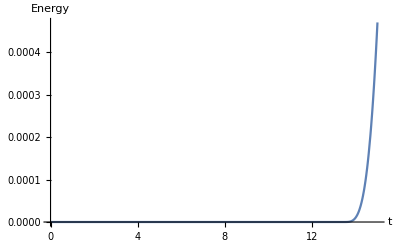

```mathematica
zGuess = L/2.;xGuess = 0.;
yGuess =FindRoot[h0+0.01*h0-fieldMagCar[xGuess,y,zGuess],{y,0.6},AccuracyGoal->20][[1]][[2]];
(*tFinal = (2.*π)/RealAbs[Im[vals[[3]]]];*)
tFinal = 15.;
(*Eqn1SigmaMinus=x'[t]==(Sqrt[mutilde]*bCrossGradModB[x[t],y[t],z[t]][[1]])/tildeBpar[x[t],y[t],z[t],0.];
Eqn2SigmaMinus=y'[t]==(Sqrt[mutilde]*bCrossGradModB[x[t],y[t],z[t]][[2]])/tildeBpar[x[t],y[t],z[t],0.];
Eqn3SigmaMinus=z'[t]==(Sqrt[mutilde]*bCrossGradModB[x[t],y[t],z[t]][[3]])/tildeBpar[x[t],y[t],z[t],0.];*)
Eqn1SigmaMinus=x'[t]==(vpar[t]*fieldCar[x[t],y[t],z[t]][[1]]+ Sqrt[mutilde]*bCrossGradModB[x[t],y[t],z[t]][[1]])/fieldMagCar[x[t],y[t],z[t]];
Eqn2SigmaMinus=y'[t]==(vpar[t]*fieldCar[x[t],y[t],z[t]][[2]]+ Sqrt[mutilde]*bCrossGradModB[x[t],y[t],z[t]][[2]])/fieldMagCar[x[t],y[t],z[t]];
Eqn3SigmaMinus=z'[t]==(vpar[t]*fieldCar[x[t],y[t],z[t]][[3]]+ Sqrt[mutilde]*bCrossGradModB[x[t],y[t],z[t]][[3]])/fieldMagCar[x[t],y[t],z[t]];
Eqn4SigmaMinus =vpar'[t]==-Dot[fieldCar[x[t],y[t],z[t]],gradModB[x[t],y[t],z[t]]]/fieldMagCar[x[t],y[t],z[t]];
(*po=First@NDSolve[{Eqn1SigmaMinus,Eqn2SigmaMinus,Eqn3SigmaMinus,Eqn4SigmaMinus,x[0]==xGuess,y[0]==yGuess,z[0]==zGuess,vpar[0]==0.,WhenEvent[(x[t]-xGuess)^2+(y[t]-yGuess)^2+(z[t]-zGuess)^2==0,{time2vparzero=t,Print[t]}]},{x[t],y[t],z[t],vpar[t]},{t,0,tFinal},MaxStepSize->0.001,Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients, "StiffnessTest"->False}];*)
po=First@NDSolve[{Eqn1SigmaMinus,Eqn2SigmaMinus,Eqn3SigmaMinus,Eqn4SigmaMinus,x[0]==xGuess,y[0]==yGuess,z[0]==zGuess,vpar[0]==0.,WhenEvent[(x[t]-xGuess)^2+(y[t]-yGuess)^2+(z[t]-zGuess)^2<10.^-8,{"StopIntegration",time2fullPer=t,Print[t]}]},{x[t],y[t],z[t],vpar[t]},{t,tFinal},MaxStepSize->0.001];
(*po=First@NDSolve[{Eqn1SigmaMinus,Eqn2SigmaMinus,Eqn3SigmaMinus,Eqn4SigmaMinus,x[0]==xGuess,y[0]==yGuess,z[0]==zGuess,vpar[0]==0.},{x[t],y[t],z[t],vpar[t]},{t,0,tFinal},Method->{"SymplecticPartitionedRungeKutta", "DifferenceOrder"->2,"PositionVariables"->{x[t],y[t]}}];*)
(*ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,tFinal},AxesLabel->{x,y},LabelStyle->{20,GrayLevel[0]}]*)
poPlot3d=ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.po],{t,0,tFinal},AxesLabel->{x,y,z},PlotRange->{{-1,1},{-1,1},{-1,1}},LabelStyle->{20,GrayLevel[0]},PlotStyle->Directive[Blue,Thickness[0.005]]];
Show[cplot3d,poPlot3d,PlotRange->{{-fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2],fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2]},{-fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2],fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2]},{0.8,1.2}}]
Plot[h0+0.01*h0-(0.5*vpar[t]^2+fieldMagCar[x[t],y[t],z[t]])/.po,{t,0,tFinal},AxesLabel->{t,"Energy"}](*PlotRange->{{0,tFinal},{-10.^-10,10.^-10}},*)
```

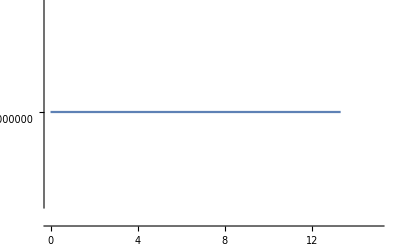

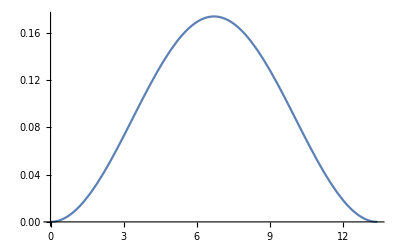

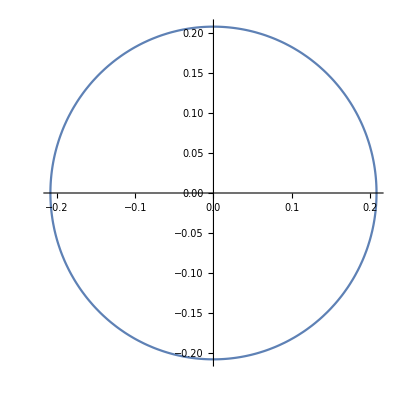

{{0.,0.0001},{0.208339,0.208339},{1.,1.},{0.,-1.13459×10^-15}}

0.0001

```mathematica
Plot[z[t]/.po,{t,0,tFinal},PlotRange->{{0,tFinal},{1-10.^-15,1+10.^-15}}]
Plot[(x[t]-xGuess)^2+(y[t]-yGuess)^2+(z[t]-zGuess)^2/.po,{t,0,time2fullPer}]
ParametricPlot[{x[t],y[t]}/.po,{t, 0, time2fullPer}]
{x[t],y[t],z[t],vpar[t]}/.po/.t->{0,time2fullPer}
Norm[{xGuess,yGuess,zGuess,0.}-{x[t],y[t],z[t],vpar[t]}/.po/.t->time2fullPer]
```

### Solving the FGCM and its variational equations

```mathematica
(*jacobianEOM=D[{Eqn1[[2]],Eqn2[[2]],Eqn3[[2]],Eqn4[[2]]},{{x[t],y[t],z[t],vpar[t]}}];
phiDot=Flatten[Table[ϕ[i,j]'[t],{i,4},{j,4}]]==Flatten[jacobianEOM.Table[ϕ[i,j][t],{i,4},{j,4}]];
stmvf=Join[{Eqn1[[1]],Eqn2[[1]],Eqn3[[1]],Eqn4[[1]]},Flatten[Table[ϕ[i,j]'[t],{i,4},{j,4}]]]==Join[{Eqn1[[2]],Eqn2[[2]],Eqn3[[2]],Eqn4[[2]]},Flatten[jacobianEOM.Table[ϕ[i,j][t],{i,4},{j,4}]]];
ics = Join[{x[0],y[0],z[0],vpar[0]},Flatten[Table[ϕ[i,j][0],{i,4},{j,4}]]]==Join[{xGuess,yGuess,zGuess,0.},Flatten[IdentityMatrix[4,WorkingPrecision->MachinePrecision]]];
vars = Join[{x,y,z,vpar},Flatten[Table[ϕ[i,j],{i,4},{j,4}]]];
sol =NDSolve[{stmvf,ics,WhenEvent[vpar[t]==0,{tEvent=t,Print[tEvent]}]},vars,{t,0,tFinal},MaxStepSize->0.1,AccuracyGoal->10,PrecisionGoal->10,Method->"ExplicitRungeKutta"]*)
(*tFinal = (2.*π)/RealAbs[Im[vals[[3]]]];*)
tFinal = time2fullPer;
jacobianEOM=D[{Eqn1SigmaMinus[[2]],Eqn2SigmaMinus[[2]],Eqn3SigmaMinus[[2]],Eqn4SigmaMinus[[2]]},{{x[t],y[t],z[t],vpar[t]}}];
phiDot=Flatten[Table[ϕ[i,j]'[t],{i,4},{j,4}]]==Flatten[jacobianEOM.Table[ϕ[i,j][t],{i,4},{j,4}]];
stmvf=Join[{Eqn1SigmaMinus[[1]],Eqn2SigmaMinus[[1]],Eqn3SigmaMinus[[1]],Eqn4SigmaMinus[[1]]},Flatten[Table[ϕ[i,j]'[t],{i,4},{j,4}]]]==Join[{Eqn1SigmaMinus[[2]],Eqn2SigmaMinus[[2]],Eqn3SigmaMinus[[2]],Eqn4SigmaMinus[[2]]},Flatten[jacobianEOM.Table[ϕ[i,j][t],{i,4},{j,4}]]];
ics = Join[{x[0],y[0],z[0],vpar[0]},Flatten[Table[ϕ[i,j][0],{i,4},{j,4}]]]==Join[{xGuess,yGuess,zGuess,0.},Flatten[IdentityMatrix[4]]];
vars = Join[{x,y,z,vpar},Flatten[Table[ϕ[i,j],{i,4},{j,4}]]];
sol =NDSolve[{stmvf,ics},vars,{t,0,tFinal},MaxStepSize->0.001,AccuracyGoal->16,Method->{"ExplicitRungeKutta","DifferenceOrder"->4}]
(*sol =NDSolve[{stmvf,ics,WhenEvent[vpar[t]==0,{tEvent=t,Print[tEvent]}]},vars,{t,0,tFinal},MaxStepSize->0.001,AccuracyGoal->16,Method->{"ExplicitRungeKutta","DifferenceOrder"->4}]*)
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],z→InterpolatingFunction[…],vpar→InterpolatingFunction[…],ϕ[1,1]→InterpolatingFunction[…],ϕ[1,2]→InterpolatingFunction[…],ϕ[1,3]→InterpolatingFunction[…],ϕ[1,4]→InterpolatingFunction[…],ϕ[2,1]→InterpolatingFunction[…],ϕ[2,2]→InterpolatingFunction[…],ϕ[2,3]→InterpolatingFunction[…],ϕ[2,4]→InterpolatingFunction[…],ϕ[3,1]→InterpolatingFunction[…],ϕ[3,2]→InterpolatingFunction[…],ϕ[3,3]→InterpolatingFunction[…],ϕ[3,4]→InterpolatingFunction[…],ϕ[4,1]→InterpolatingFunction[…],ϕ[4,2]→InterpolatingFunction[…],ϕ[4,3]→InterpolatingFunction[…],ϕ[4,4]→InterpolatingFunction[…]}}

```mathematica
Eigensystem[Table[ϕ[i,j][t],{i,4},{j,4}]/.sol/.{t->tFinal}]
```

{{3.81125×10^8,1.01612,0.984135,-1.1455×10^-8},{{-1.31084×10^-9,-2.96915×10^-10,0.563171,0.826341},{-0.999543,0.0302338,1.09609×10^-10,-1.62092×10^-10},{-0.999557,-0.0297541,2.80777×10^-11,-4.15218×10^-11},{-2.5262×10^-8,-1.56191×10^-8,-0.560164,0.828382}}}

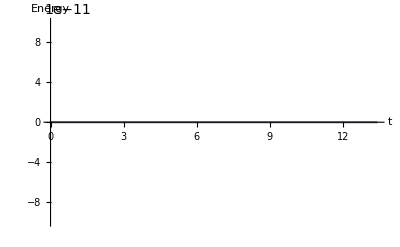

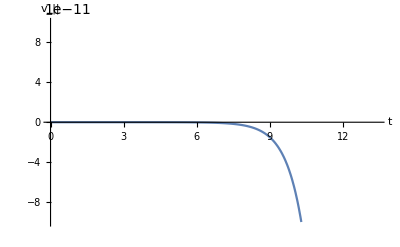

-Graphics3D-

```mathematica
Plot[h0+0.01*h0-(0.5*vpar[t]^2+fieldMagCar[x[t],y[t],z[t]])/.sol,{t,0,tFinal},PlotRange->{{0,tFinal},{-10.^-10,10.^-10}},AxesLabel->{t,"Energy"}]
Plot[vpar[t]/.sol,{t,0,tFinal},PlotRange->{{0,tFinal},{-10.^-10,10.^-10}},AxesLabel->{t,"v_||"}]
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sol],{t,0,tFinal},AxesLabel->{x,y,z},PlotRange->{{-1,1},{-1,1},{-1,1}},LabelStyle->{20,GrayLevel[0]}]
(*ParametricPlot[{x[t],y[t]}/.sol,{t,0,tFinal}]
Plot[h0+0.01*h0-(0.5*vpar[t]^2+fieldMagCar[x[t],y[t],z[t]])/.sol,{t,0,tFinal},PlotRange->{{0,tFinal},{-10.^-4,10.^-4}},AxesLabel->{t,"Energy"}]
Plot[vpar[t]/.sol,{t,0,tFinal}]*)
```

### Differential correction of the hyperbolic PO

```mathematica
(*smallAmp1=10.^-3;
initCondGuess = eqpt[[All,2]]+smallAmp1*Re[vecs[[3]]]
timePerGuess = (2*π)/Im[vals[[3]]]
sol=First@NDSolve[{Eqn1,Eqn2,Eqn3,Eqn4,x[0]==initCondGuess[[1]],y[0]==initCondGuess[[2]],z[0]==initCondGuess[[3]],vpar[0]==initCondGuess[[4]]},{x[t],y[t],z[t],vpar[t]},{t,0,timePerGuess}]
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sol],{t,0,timePerGuess},AxesLabel->{x,y,z},PlotRange->{{-1,1},{-1,1},{-1,1}},LabelStyle->{20,GrayLevel[0]}]*)
DOPRIamat={
{1/5},
{3/40,9/40},
{44/45,-56/15,32/9},
{19372/6561,-25360/2187,64448/6561,-212/729},
{9017/3168,-355/33,46732/5247,49/176,-5103/18656},
{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84, 0};
DOPRIcvec = {1/5,3/10,4/5,8/9,1, 1};
DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DOPRICoefficients[5, p_]:=
N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec}, p];
zGuess = L/2.;xGuess = 0.;
yGuess =FindRoot[h0+0.01*h0-fieldMagCar[xGuess,y,zGuess],{y,0.6},AccuracyGoal->20][[1]][[2]];
vparGuess=0.;
(*tFinal = (2.*π)/RealAbs[Im[vals[[3]]]]*)
jacobianEOM=D[{Eqn1SigmaMinus[[2]],Eqn2SigmaMinus[[2]],Eqn3SigmaMinus[[2]],Eqn4SigmaMinus[[2]]},{{x[t],y[t],z[t],vpar[t]}}];
phiDot=Flatten[Table[ϕ[i,j]'[t],{i,4},{j,4}]]==Flatten[jacobianEOM.Table[ϕ[i,j][t],{i,4},{j,4}]];
stmvf=Join[{Eqn1SigmaMinus[[1]],Eqn2SigmaMinus[[1]],Eqn3SigmaMinus[[1]],Eqn4SigmaMinus[[1]]},Flatten[Table[ϕ[i,j]'[t],{i,4},{j,4}]]]==Join[{Eqn1SigmaMinus[[2]],Eqn2SigmaMinus[[2]],Eqn3SigmaMinus[[2]],Eqn4SigmaMinus[[2]]},Flatten[jacobianEOM.Table[ϕ[i,j][t],{i,4},{j,4}]]];
tpGuess = (2.*π)/RealAbs[Im[vals[[3]]]];
tFinal =0.5tpGuess;
maxIter = 10;numIter=0;maxdydot=10.^-30;
vparDot1=1; (*this assumes the guess initial condition is within 1 unit of the correct initial condition*)
While[numIter<maxIter&& Abs[vparDot1]>maxdydot,
initCondGuess = {xGuess,yGuess,zGuess,vparGuess};
vfSol=First@NDSolve[{Eqn1SigmaMinus,Eqn2SigmaMinus,Eqn3SigmaMinus,Eqn4SigmaMinus,x[0]==initCondGuess[[1]],y[0]==initCondGuess[[2]],z[0]==initCondGuess[[3]],vpar[0]==initCondGuess[[4]],WhenEvent[x[t]==0.,{"Stop Integration",tEvent=t}]},{x[t],y[t],z[t],vpar[t]},{t,0,tFinal},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients, "StiffnessTest"->True}];
{x1,y1,z1,vpar1}={x[t],y[t],z[t],vpar[t]}/.vfSol/.t->tEvent;
Print[numIter,"   ",vparDot1,"   ",{xGuess,SetPrecision[yGuess,20],zGuess,vparGuess}];
ics = Join[{x[0],y[0],z[0],vpar[0]},Flatten[Table[ϕ[i,j][0],{i,4},{j,4}]]]==Join[{xGuess,yGuess,zGuess,0.},Flatten[IdentityMatrix[4]]];
vars = Join[{x,y,z,vpar},Flatten[Table[ϕ[i,j],{i,4},{j,4}]]];
stmvfSol=First@NDSolve[{stmvf,ics},vars,{t,0,tEvent},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients, "StiffnessTest"->True}];
phiMat1=Table[ϕ[i,j][t],{i,4},{j,4}]/.stmvfSol/.{t->tEvent};
xDot1=Eqn1SigmaMinus[[2]]/.{x[t]->x1,y[t]->y1,z[t]->z1,vpar[t]->vpar1};
yDot1=Eqn2SigmaMinus[[2]]/.{x[t]->x1,y[t]->y1,z[t]->z1,vpar[t]->vpar1};
zDot1=Eqn3SigmaMinus[[2]]/.{x[t]->x1,y[t]->y1,z[t]->z1,vpar[t]->vpar1};
vparDot1=Eqn4SigmaMinus[[2]]/.{x[t]->x1,y[t]->y1,z[t]->z1,vpar[t]->vpar1};
(*yGuessCorr =yDot1/(phiMat1[[4]][[2]]-phiMat1[[3]][[2]]*(zDot1/vparDot1));*)
yGuessCorr=((vpar1-0.)/(1.-phiMat1[[2]][[2]]))*(yDot1/vparDot1);
(*yGuessCorr =(x1-xDot1*(vpar1/vparDot1))/phiMat1[[1]][[2]];*)
Print[yGuessCorr];
yGuess = yGuess-yGuessCorr;
numIter++]
(*sol=First@NDSolve[{Eqn1,Eqn2,Eqn3,Eqn4,x[0]==initCondGuess[[1]],y[0]==initCondGuess[[2]],z[0]==initCondGuess[[3]],vpar[0]==initCondGuess[[4]]},{x[t],y[t],z[t],vpar[t]},{t,0,tFinal}]
ParametricPlot[{Sqrt[x[t]^2 + y[t]^2],z[t]}/.sol,{t,0,tFinal},AxesLabel->{r,z},LabelStyle->{20,GrayLevel[0]}]*)
```

0   1   {0.,0.20833925019950599866,1.,0.}

-2.50064×10^-11

1   -7.48203×10^-13   {0.,0.20833925022451241227,1.,0.}

-2.50064×10^-11

2   -7.48203×10^-13   {0.,0.20833925024951885363,1.,0.}

-2.50065×10^-11

3   -7.48203×10^-13   {0.,0.20833925027452532275,1.,0.}

-2.50065×10^-11

4   -7.48203×10^-13   {0.,0.20833925029953176411,1.,0.}

-2.50064×10^-11

5   -7.48203×10^-13   {0.,0.20833925032453820547,1.,0.}

-2.50065×10^-11

6   -7.48203×10^-13   {0.,0.20833925034954467459,1.,0.}

-2.50065×10^-11

7   -7.48203×10^-13   {0.,0.20833925037455114371,1.,0.}

-2.50064×10^-11

8   -7.48203×10^-13   {0.,0.20833925039955755731,1.,0.}

-2.50064×10^-11

9   -7.48203×10^-13   {0.,0.20833925042456399868,1.,0.}

-2.50065×10^-11

```mathematica
phiMat1//MatrixForm
{vals,vecs}=Eigensystem[phiMat1]
Re[vecs[[1]]]
Norm[Re[vecs[[1]]]]
```

(-1. | 0.266739 | 6.0059×10^-10 | 4.06128×10^-10
-4.46168×10^-11 | -1. | -2.66412×10^-10 | -1.80152×10^-10
-2.63124×10^-14 | -1.56204×10^-12 | 10072.8 | 6811.35
-4.9035×10^-14 | -2.5468×10^-12 | 14895.8 | 10072.8)

{{20145.5,-1.+3.44979×10^-6 ⅈ,-1.-3.44979×10^-6 ⅈ,0.0000496389},{{-3.36295×10^-14+0. ⅈ,1.46655×10^-14+0. ⅈ,-0.560164+0. ⅈ,-0.828382+0. ⅈ},{1.+0. ⅈ,4.57354×10^-11+0.0000129332 ⅈ,-3.50478×10^-15-1.08328×10^-18 ⅈ,4.98438×10^-15+1.60874×10^-18 ⅈ},{1.+0. ⅈ,4.57354×10^-11-0.0000129332 ⅈ,-3.50478×10^-15+1.08328×10^-18 ⅈ,4.98438×10^-15-1.60874×10^-18 ⅈ},{-5.64448×10^-13+0. ⅈ,1.6663×10^-13+0. ⅈ,-0.560164+0. ⅈ,0.828382+0. ⅈ}}}

{-3.36295×10^-14,1.46655×10^-14,-0.560164,-0.828382}

1.

#### Globalising the backward contracting (unstable) manifold

```mathematica
po=First@NDSolve[{Eqn1SigmaMinus,Eqn2SigmaMinus,Eqn3SigmaMinus,Eqn4SigmaMinus,x[0]==xGuess,y[0]==yGuess,z[0]==zGuess,vpar[0]==0.},{x[t],y[t],z[t],vpar[t]},{t,0,tpGuess},MaxStepSize->0.001,Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients, "StiffnessTest"->True}];
ics = Join[{x[0],y[0],z[0],vpar[0]},Flatten[Table[ϕ[i,j][0],{i,4},{j,4}]]]==Join[{xGuess,yGuess,zGuess,0.},Flatten[IdentityMatrix[4]]];
vars = Join[{x,y,z,vpar},Flatten[Table[ϕ[i,j],{i,4},{j,4}]]];
stmvfSol=First@NDSolve[{stmvf,ics},vars,{t,0,tpGuess},MaxStepSize->0.001,Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients, "StiffnessTest"->True}];
numTrajMani = 20;
idxTrajMani=1;
ti=0;deltati =tpGuess/numTrajMani;
uManiInitCond=ConstantArray[0,{numTrajMani,4}];
dir = 1;(*which branch of the manifold*)
del=10.^-8;
While[idxTrajMani<=numTrajMani && ti<tpGuess,
(*phiMat1=Table[ϕ[i,j][t],{i,4},{j,4}]/.stmvfSol/.{t->ti};*)
uManiInitCond[[idxTrajMani]]={x[t],y[t],z[t],vpar[t]}+dir*del*Re[vecs[[1]]]/.po/.{t->ti};
idxTrajMani++;ti=ti+deltati;]
Print[uManiInitCond//MatrixForm];
tFinalMani = 10*tpGuess;
ti=0;
uManiPlot3d=CreateDataStructure["DynamicArray"];
uManiIntersectParVel0 = ConstantArray[0,{idxTrajMani-1,4}];
For[idx=1,idx<idxTrajMani,idx++,
(*phiMat1=Table[ϕ[i,j][t],{i,4},{j,4}]/.stmvfSol/.{t->ti+deltati};*)
Print[idx,": ",uManiInitCond[[idx]]];
uManiTraj=First@NDSolve[{Eqn1,Eqn2,Eqn3,Eqn4,x[0]==uManiInitCond[[idx]][[1]],y[0]==uManiInitCond[[idx]][[2]],z[0]==uManiInitCond[[idx]][[3]],vpar[0]==uManiInitCond[[idx]][[4]],WhenEvent[vpar[t]==0,{"StopIntegration",time2vparzero=t,uManiIntersectParVel0[[idx]]={x[t],y[t],z[t],vpar[t]},Print[t]}]},{x[t],y[t],z[t],vpar[t]},{t,0,tFinalMani},MaxStepSize->0.001,Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients, "StiffnessTest"->True}];
uManiPlot3d["Append",ParametricPlot3D[{x[t],y[t],z[t]}/.uManiTraj,{t,0,time2vparzero},AxesLabel->{x,y,z},PlotRange->{{-1,1},{-1,1},{-1,1}},LabelStyle->{20,GrayLevel[0]},PlotStyle->Directive[Magenta,Thickness[0.005]]]]
]
(*]*)
(*po=First@NDSolve[{Eqn1SigmaMinus,Eqn2SigmaMinus,Eqn3SigmaMinus,Eqn4SigmaMinus,x[0]==xGuess,y[0]==yGuess,z[0]==zGuess,vpar[0]==0.},{x[t],y[t],z[t],vpar[t]},{t,0,tFinal},Method->{"SymplecticPartitionedRungeKutta", "DifferenceOrder"->2,"PositionVariables"->{x[t],y[t]}}];*)
(*ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,tFinal},AxesLabel->{x,y},LabelStyle->{20,GrayLevel[0]}]*)
```

(-3.36295×10^-22 | 0.208339 | 1. | -8.28382×10^-9
-0.0671176 | 0.197232 | 1. | -8.28382×10^-9
-0.127079 | 0.165095 | 1. | -8.28382×10^-9
-0.17349 | 0.115354 | 1. | -8.28382×10^-9
-0.201402 | 0.0533135 | 1. | -8.28382×10^-9
-0.20784 | -0.0144117 | 1. | -8.28382×10^-9
-0.192117 | -0.0806001 | 1. | -8.28383×10^-9
-0.155909 | -0.138194 | 1. | -8.28385×10^-9
-0.103077 | -0.181054 | 1. | -8.28392×10^-9
-0.0392539 | -0.204608 | 1. | -8.28411×10^-9
0.0287543 | -0.206345 | 1. | -8.28463×10^-9
0.0936966 | -0.186081 | 1. | -8.28609×10^-9
0.148648 | -0.145976 | 1. | -8.29014×10^-9
0.18775 | -0.0903055 | 1. | -8.30144×10^-9
0.206833 | -0.0250064 | 1. | -8.33293×10^-9
0.203862 | 0.0429592 | 1. | -8.42086×10^-9
0.179154 | 0.106344 | 1. | -8.66682×10^-9
0.135343 | 0.15839 | 1. | -9.35643×10^-9
0.0771018 | 0.193547 | 1. | -1.12945×10^-8
0.010639 | 0.208067 | 1. | -1.67532×10^-8)

1: {-3.36295×10^-22,0.208339,1.,-8.28382×10^-9}

106.188

2: {-0.0671176,0.197232,1.,-8.28382×10^-9}

3: {-0.127079,0.165095,1.,-8.28382×10^-9}

33.5109

4: {-0.17349,0.115354,1.,-8.28382×10^-9}

5: {-0.201402,0.0533135,1.,-8.28382×10^-9}

27.5718

6: {-0.20784,-0.0144117,1.,-8.28382×10^-9}

7: {-0.192117,-0.0806001,1.,-8.28383×10^-9}

22.0357

8: {-0.155909,-0.138194,1.,-8.28385×10^-9}

23.3085

9: {-0.103077,-0.181054,1.,-8.28392×10^-9}

16.1702

10: {-0.0392539,-0.204608,1.,-8.28411×10^-9}

15.9229

11: {0.0287543,-0.206345,1.,-8.28463×10^-9}

15.8121

12: {0.0936966,-0.186081,1.,-8.28609×10^-9}

15.7663

13: {0.148648,-0.145976,1.,-8.29014×10^-9}

15.7662

14: {0.18775,-0.0903055,1.,-8.30144×10^-9}

15.8052

15: {0.206833,-0.0250064,1.,-8.33293×10^-9}

15.8835

16: {0.203862,0.0429592,1.,-8.42086×10^-9}

16.0109

17: {0.179154,0.106344,1.,-8.66682×10^-9}

16.2315

18: {0.135343,0.15839,1.,-9.35643×10^-9}

17.39

19: {0.0771018,0.193547,1.,-1.12945×10^-8}

34.0989

20: {0.010639,0.208067,1.,-1.67532×10^-8}

105.921

```mathematica
Show[cplot3d,poPlot3d,Table[uManiPlot3d["Part",idx],{idx,1,numTrajMani}],PlotRange->{{-0.8*fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2],0.8*fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2]},{-0.8*fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2],0.8*fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2]},{-1,1}},AxesLabel->{Style[x,25],Style[y,25],Style[z,25]},AxesStyle->Directive[Gray,FontSize->15],ImageSize->500]
```

-Graphics3D-

#### Globalising the forward contracting (stable) manifold

```mathematica
numTrajMani = 20;
idxTrajMani=1;
dir = 1;
del=10.^-8;
ti=0;deltati =tpGuess/numTrajMani;
sManiInitCond=ConstantArray[0,{numTrajMani,4}];
While[idxTrajMani<=numTrajMani && ti<tpGuess,
sManiInitCond[[idxTrajMani]]={x[t],y[t],z[t],vpar[t]}+dir*del*Re[vecs[[4]]]/.po/.{t->ti};
idxTrajMani++;
ti=ti+deltati;]
Print[sManiInitCond//MatrixForm]
tFinalMani = 10.*tpGuess;
ti=0;
sManiPlot3d=CreateDataStructure["DynamicArray"];
sManiIntersectParVel0 = ConstantArray[0,{idxTrajMani-1,4}];
For[idx=1,idx<idxTrajMani,idx++,
(*phiMat1=Table[ϕ[i,j][t],{i,4},{j,4}]/.stmvfSol/.{t->ti+deltati};*)
Print[idx,": ",sManiInitCond[[idx]]];
sManiTraj=First@NDSolve[{Eqn1,Eqn2,Eqn3,Eqn4,x[0]==sManiInitCond[[idx]][[1]],y[0]==sManiInitCond[[idx]][[2]],z[0]==sManiInitCond[[idx]][[3]],vpar[0]==sManiInitCond[[idx]][[4]],WhenEvent[vpar[t]==0,{"StopIntegration",time2vparzero=t,sManiIntersectParVel0[[idx]]={x[t],y[t],z[t],vpar[t]},Print["Bounce time: ",t]}]},{x[t],y[t],z[t],vpar[t]},{t,-tFinalMani,0},MaxStepSize->0.001,Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients, "StiffnessTest"->True}];
sManiPlot3d["Append",ParametricPlot3D[{x[t],y[t],z[t]}/.sManiTraj,{t,time2vparzero,0},AxesLabel->{x,y,z},PlotRange->{{-1,1},{-1,1},{-1,1}},LabelStyle->{20,GrayLevel[0]},PlotStyle->Directive[Green,Thickness[0.005]]]]
]
```

(-5.64448×10^-21 | 0.208339 | 1. | 8.28382×10^-9
-0.0671176 | 0.197232 | 1. | 8.28382×10^-9
-0.127079 | 0.165095 | 1. | 8.28382×10^-9
-0.17349 | 0.115354 | 1. | 8.28382×10^-9
-0.201402 | 0.0533135 | 1. | 8.28381×10^-9
-0.20784 | -0.0144117 | 1. | 8.28381×10^-9
-0.192117 | -0.0806001 | 1. | 8.2838×10^-9
-0.155909 | -0.138194 | 1. | 8.28378×10^-9
-0.103077 | -0.181054 | 1. | 8.28371×10^-9
-0.0392539 | -0.204608 | 1. | 8.28352×10^-9
0.0287543 | -0.206345 | 1. | 8.283×10^-9
0.0936966 | -0.186081 | 1. | 8.28155×10^-9
0.148648 | -0.145976 | 1. | 8.27749×10^-9
0.18775 | -0.0903055 | 1. | 8.26619×10^-9
0.206833 | -0.0250064 | 1. | 8.2347×10^-9
0.203862 | 0.0429592 | 1. | 8.14677×10^-9
0.179154 | 0.106344 | 1. | 7.90082×10^-9
0.135343 | 0.15839 | 1. | 7.2112×10^-9
0.0771018 | 0.193547 | 1. | 5.27311×10^-9
0.010639 | 0.208067 | 1. | -1.85554×10^-10)

1: {-5.64448×10^-21,0.208339,1.,8.28382×10^-9}

Bounce time: -15.849

2: {-0.0671176,0.197232,1.,8.28382×10^-9}

Bounce time: -16.0015

3: {-0.127079,0.165095,1.,8.28382×10^-9}

Bounce time: -16.4018

4: {-0.17349,0.115354,1.,8.28382×10^-9}

Bounce time: -22.3713

5: {-0.201402,0.0533135,1.,8.28381×10^-9}

Bounce time: -22.0254

6: {-0.20784,-0.0144117,1.,8.28381×10^-9}

Bounce time: -28.131

7: {-0.192117,-0.0806001,1.,8.2838×10^-9}

Bounce time: -27.5474

8: {-0.155909,-0.138194,1.,8.28378×10^-9}

Bounce time: -34.3815

9: {-0.103077,-0.181054,1.,8.28371×10^-9}

Bounce time: -33.5384

10: {-0.0392539,-0.204608,1.,8.28352×10^-9}

Bounce time: -111.56

11: {0.0287543,-0.206345,1.,8.283×10^-9}

Bounce time: -101.84

12: {0.0936966,-0.186081,1.,8.28155×10^-9}

Bounce time: -34.3642

13: {0.148648,-0.145976,1.,8.27749×10^-9}

Bounce time: -16.8434

14: {0.18775,-0.0903055,1.,8.26619×10^-9}

Bounce time: -16.1904

15: {0.206833,-0.0250064,1.,8.2347×10^-9}

Bounce time: -15.9813

16: {0.203862,0.0429592,1.,8.14677×10^-9}

Bounce time: -15.862

17: {0.179154,0.106344,1.,7.90082×10^-9}

Bounce time: -15.7923

18: {0.135343,0.15839,1.,7.2112×10^-9}

Bounce time: -15.7628

19: {0.0771018,0.193547,1.,5.27311×10^-9}

Bounce time: -15.774

20: {0.010639,0.208067,1.,-1.85554×10^-10}

Bounce time: -0.00752237

```mathematica
Show[cplot3d,poPlot3d,Table[sManiPlot3d["Part",idx],{idx,1,numTrajMani}],Table[uManiPlot3d["Part",idx],{idx,1,numTrajMani}],PlotRange->{{-0.8*fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2],0.8*fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2]},{-0.8*fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2],0.8*fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2]},{-1,1}},AxesLabel->{Style[x,25],Style[y,25],Style[z,25]},AxesStyle->Directive[Gray,FontSize->15],ImageSize->500]
```

-Graphics3D-

```mathematica
Show[cplot3d,ListLinePlot3D[sManiIntersectParVel0[[All,1;;3]],PlotStyle->Directive[Green,Thickness[0.01]]],ListLinePlot3D[uManiIntersectParVel0[[All,1;;3]],PlotStyle->Directive[Magenta,Thickness[0.01]]],PlotRange->{{-0.8*fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2],0.8*fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2]},{-0.8*fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2],0.8*fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2]},{-0.75,-0.25}},AxesLabel->{Style[x,25],Style[y,25],Style[z,25]},AxesStyle->Directive[Gray,FontSize->15],ImageSize->500]
```

```mathematica
sManiIntersectParVel0[[All,1;;4]]
uManiIntersectParVel0[[All,1;;4]]
```

{{-0.0223069,0.215489,-0.958947,7.62872×10^-17},{-0.0727739,0.200942,-0.967057,-6.56518×10^-17},{-0.0972974,0.186121,-0.981653,3.06457×10^-18},{0.139182,0.165558,-2.95984,1.68932×10^-17},{0.0488428,0.206085,-2.97364,-8.3653×10^-18},{0.211177,0.0243767,-4.97077,1.48197×10^-17},{0.161273,0.134808,-4.9807,-6.863×10^-17},{0.13636,-0.157792,-6.99353,4.51028×10^-17},{0.206584,-0.029676,-6.99146,-3.04754×10^-17},{0.124938,-0.166726,-32.9991,-1.00787×10^-17},{0.0432735,0.205684,-28.9807,1.04111×10^-16},{0.186686,0.0934341,-6.9908,-3.28496×10^-17},{0.102645,-0.181832,-0.990364,-1.22142×10^-17},{0.192617,-0.087249,-0.974969,-1.34339×10^-17},{0.214016,-0.00108591,-0.966127,-1.58565×10^-17},{0.201714,0.0781003,-0.959795,-4.25041×10^-17},{0.164342,0.143291,-0.955567,-5.58161×10^-17},{0.110227,0.189111,-0.95362,-4.64072×10^-17},{0.0481685,0.213213,-0.954306,5.26177×10^-17},{0.011372,0.208029,1.,-1.21169×10^-26}}

{{0.185854,-0.0944891,-30.9944,7.34721×10^-17},{0,0,0,0},{0.201657,0.0548865,-6.98856,-5.79006×10^-17},{0,0,0,0},{0.180263,-0.111194,-4.97362,-7.74518×10^-17},{0,0,0,0},{0.0771794,-0.199687,-2.96593,-7.0668×10^-18},{0.204774,-0.0669828,-2.96205,-1.40801×10^-16},{-0.0927261,-0.190245,-0.974237,1.52263×10^-17},{-0.0532899,-0.208363,-0.963089,5.47217×10^-17},{0.00252296,-0.217531,-0.956729,-6.4693×10^-17},{0.0649407,-0.20893,-0.953845,2.31274×10^-17},{0.125736,-0.179024,-0.953896,-3.67409×10^-17},{0.1762,-0.127774,-0.956475,8.04207×10^-17},{0.207657,-0.0585393,-0.961242,-3.3922×10^-17},{0.212229,0.0222664,-0.968063,2.68577×10^-17},{0.181818,0.10681,-0.977458,-4.43151×10^-17},{0.0353785,0.205387,-0.996184,-7.86745×10^-18},{0.183193,-0.100405,-6.98937,4.94616×10^-17},{0.166215,-0.129299,-30.9788,-7.83099×10^-17}}

### Computing arclength of trajectories on the manifold

```mathematica
(*SetDirectory[NotebookDirectory[]]
<<ToMatlab.m
fogcODES={Eqn1,Eqn2,Eqn3,Eqn4}/.{x[t]->x,y[t]->y,z[t]->z,vpar[t]->vpar};
f=OpenWrite["fogc_odes_mmmodel1958.m"];
WriteMatlab[fogcODES,f,"function [tOut, yOut] = fogc_odes_mmmodel1958(eqpt, parameters)\nfogcODES",60]
WriteMatlab["end\n",f]
Close[f];*)
```

/Users/OptimusPrime/Documents/magnetic-mirror

```mathematica
(*SetDirectory[NotebookDirectory[]]
<<ToMatlab.m
jacobianEOM = jacobianEOM/.{x[t]->x,y[t]->y,z[t]->z,vpar[t]->vpar}
f=OpenWrite["jacobian_mmmodel1958.m"];
WriteMatlab[jacobianEOM,f,"function Df = jacobian_mmmodel1958(eqpt, parameters)\njacobianEOM",60]
WriteMatlab["end\n",f]
Close[f];*)
```

/Users/OptimusPrime/Documents/magnetic-mirror